```mathematica
NotebookDirectory[]//SetDirectory;
```

```mathematica
<<"crediblePlot.m";
```

## Recoil Spectrum

```mathematica
dRdE=Import["DS_XENON_dRdE.dat"]//Drop[#,2]&;
```

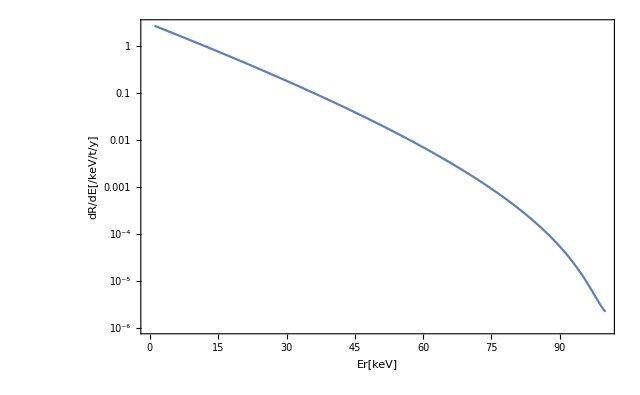

```mathematica
ListLogPlot[dRdE,Joined->True,Frame->True,FrameLabel->{"Er[keV]","dR/dE[/keV/t/y]"}]
```

## Monte-Carlo Simulations

#### Spin Independent Simulation in Xenon

```mathematica
dataMC=Import["DS_sim.dat"];
```

```mathematica
dataMC[[1;;5]]//MatrixForm
```

({//,Asimov,simulation}
{//,WIMP,pars:,spin-0.5,,Mx,=,100,,C1,=,0.0001,,C2,=,0}
{//,Detectors,used:}
{XENON,-,10,t.y,,nEvents,=,192.833}
{//,P,-2Log(L),Mx,C1,rho,v0,vesc})

1 and 2σ marginalized credible regions in the mass vs coupling plane:

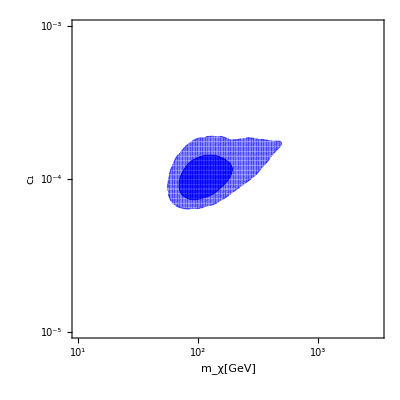

```mathematica
LogLogCrediblePlot2D[dataMC[[6;;All,{3,4,1}]],30,PlotRange->{{1,3.5},{-5,-3}},FrameLabel->{"m_χ[GeV]","c_1"}]
```

1D marginalized posterior for mass

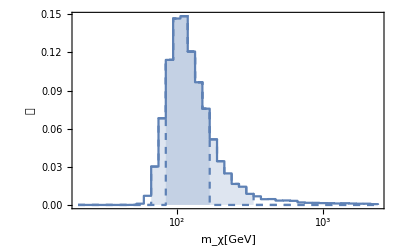

```mathematica
LogCrediblePlot1D[dataMC[[6;;All,{3,1}]],40,FrameLabel->{"m_χ[GeV]","𝒫"}]
```